((0.0666667 (2.37037×10^22 E1+(0.+9.77778×10^16 ⅈ) E1 ω-1.45556×10^12 E1 ω^2-(0.+3.2×10^6 ⅈ) E1 ω^3+1. E1 ω^4))/(((0.-2.66667×10^6 ⅈ)+1. ω) ((0.+5.33333×10^16 ⅈ)-1.45556×10^12 ω-(0.+3.2×10^6 ⅈ) ω^2+1. ω^3))
((0.+5.92593×10^14 ⅈ) E1)/((0.+5.33333×10^16 ⅈ)-1.45556×10^12 ω-(0.+3.2×10^6 ⅈ) ω^2+1. ω^3)
-(1.11111×10^9 E1 ((0.-533333. ⅈ)+1. ω))/((0.+5.33333×10^16 ⅈ)-1.45556×10^12 ω-(0.+3.2×10^6 ⅈ) ω^2+1. ω^3))

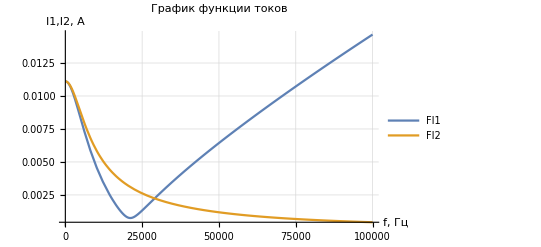

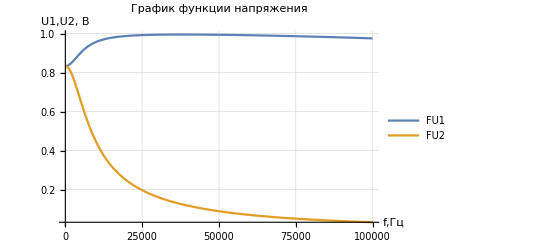

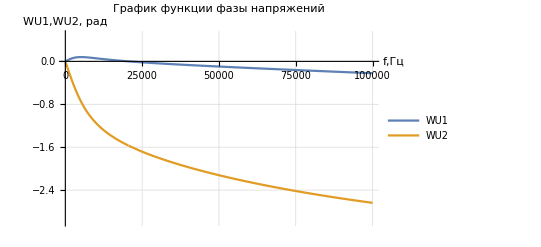

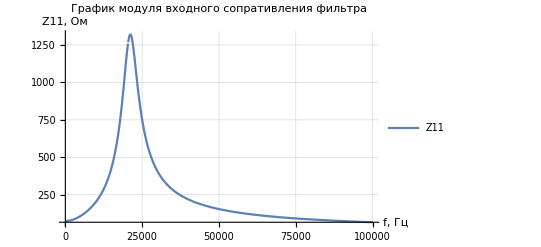

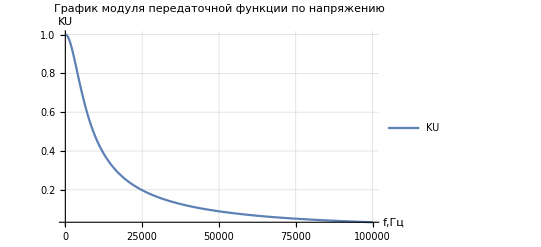

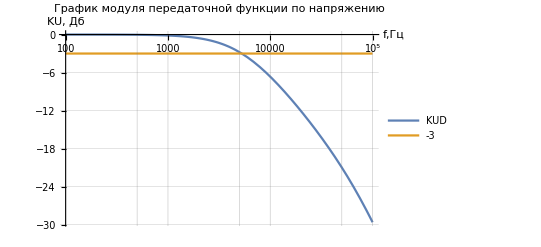

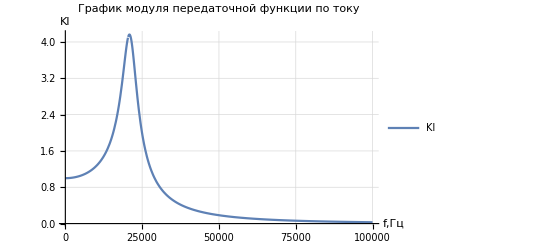

```mathematica
Clear["Global`*"]
Z1=15; Z2=75;
C0=0.025*10^-6;
L0=1.2*10^-3;
Z3=Z5=ⅈ*ω*L0;
Z4=Z6=1/(ⅈ*ω*C0);
CM=({{1, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, -1}, {0, 0, 1, -1, -1, 1}});
ZM=({{Z1, 0, 0, 0, 0, 0}, {0, Z2, 0, 0, 0, 0}, {0, 0, Z3, 0, 0, 0}, {0, 0, 0, Z4, 0, 0}, {0, 0, 0, 0, Z5, 0}, {0, 0, 0, 0, 0, Z6}});
EM=({{E1}, {0}, {0}, {0}, {0}, {0}});
CZM=CM.ZM;CZCtM=CM.ZM.Transpose[CM];
CEM=CM.EM;IM=LinearSolve[CZCtM,CEM];
IM//MatrixForm
E1=1;
ω=2*π*fr;
FI1=Extract[IM,{1}];FI2=Extract[IM,{2}];
FU1=E1-FI1*Z1;FU2=FI2*Z2;
WU1=Arg[FU1];WU2=Arg[FU2];
Wl1=Arg[FI1];Wl2=Arg[FI2];
KU=Abs[FU2/FU1];KUD=20*Log10[KU];KI=Abs[FI2/FI1];
Z11=Abs[FU1/FI1];

Plot[Evaluate[{Abs[FI1],Abs[FI2]}],{fr,100,100000},AxesLabel->TraditionalForm/@{"f, Гц","I1,I2, А"},PlotRange->All,PlotLegends-> LineLegend[{"FI1","FI2"}],PlotLabel -> Style["График функции токов",12,Black],GridLines->Automatic]

Plot[Evaluate[{Abs[FU1],Abs[FU2]}],{fr,100,100000},AxesLabel->TraditionalForm/@{"f,Гц","U1,U2, В"},PlotRange->All,PlotLegends-> LineLegend[{"FU1","FU2"}],PlotLabel -> Style["График функции напряжения",12,Black],GridLines->Automatic]

Plot[Evaluate[{WU1,WU2}],{fr,100,100000},AxesLabel->TraditionalForm/@{"f,Гц","WU1,WU2, рад"},PlotRange->{All,{-3,0.5}},PlotLegends-> LineLegend[{"WU1","WU2"}],PlotLabel -> Style["График функции фазы напряжений",12,Black],GridLines->Automatic]

Plot[Evaluate[Z11],{fr,100,100000},AxesLabel->TraditionalForm/@{"f, Гц","Z11, Ом"},PlotRange->All,PlotLegends-> LineLegend[{"Z11"}],PlotLabel -> Style["График модуля входного сопративления фильтра",12,Black],GridLines->Automatic]

Plot[Evaluate[KU],{fr,100,100000}, AxesLabel->TraditionalForm/@{"f,Гц","KU"},PlotRange->All,PlotLegends-> LineLegend[{"KU"}],PlotLabel -> Style["График модуля передаточной функции по напряжению",12,Black],GridLines->Automatic]

LogLinearPlot[Evaluate[{KUD,-3}],{fr,100,100000},AxesLabel->TraditionalForm/@{"f,Гц","KU, Дб"},PlotRange->All,PlotLegends-> LineLegend[{"KUD","-3"}],PlotLabel -> Style["График модуля передаточной функции по напряжению",12,Black],GridLines->Automatic]

Plot[Evaluate[KI],{fr,100,100000}, AxesLabel->TraditionalForm/@{"f,Гц","KI"},PlotRange->All,PlotLegends-> LineLegend[{"KI"}],PlotLabel -> Style["График модуля передаточной функции по току",12,Black],GridLines->Automatic]
```